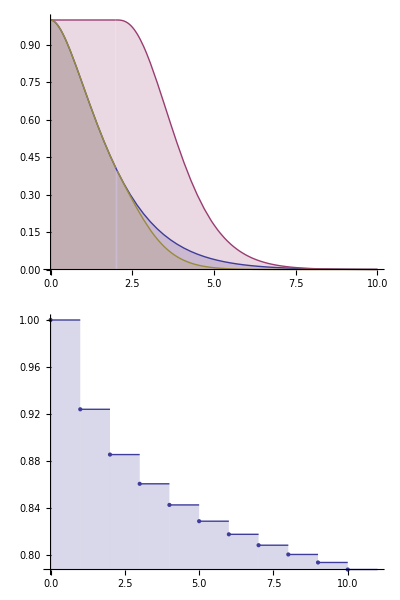

```mathematica
Clear["Global`*"]
Module[{
k=2,
q=3,
λ=1,
ν=1,
ℰ,𝒲,S,f},
ℰ=ErlangDistribution[k,λ];
𝒲=TransformedDistribution[x+2,x\[Distributed]ErlangDistribution[3,ν]];
Subscript[S, 𝒟_][t_]:=SurvivalFunction[𝒟,t];
f[k_]:=NIntegrate[PDF[ℰ,t] Subscript[S, 𝒲][t]^k,{t,0,∞}];
Column[{
Plot[{
Subscript[S, ℰ][t],
Subscript[S, 𝒲][t]^k,
Subscript[S, ℰ][t] Subscript[S, 𝒲][t]^k},
{t,0,10},
Filling->Axis,ImageSize->Large],
DiscretePlot[f[k],{k,0,10},
ExtentSize->Right,PlotMarkers->"Point"]}]]
```